```mathematica
parse[s_]:=ToExpression@StringReplace[s,{"("->"{",")"->"}","Vector("->"{","E"->"*10^"}]
```

```mathematica
fitDegree[data_]:=FindFit[data,a x^n+c,{a,n,c},x]
```

```mathematica
plotTogehter[data_, rule_]:=With[{expr=a x^n+c/.rule},
Show[
Plot[expr,{x,data[[1,1]],data[[-1,1]]}],
ListPlot[data,PlotStyle->Red],PlotLabel->expr]]
```

```mathematica
fitAndPlot[data_]:=plotTogehter[data,fitDegree[data]]
```

```mathematica
s="Vector((74.0,6530.0), (92.0,15227.0), (170.0,54570.0), (206.0,86260.0), (212.0,92423.0), (272.0,256875.0), (314.0,564271.0), (422.0,6402303.0), (428.0,6822921.0), (434.0,7624681.0), (488.0,1.3870956E7), (494.0,1.4200355E7), (506.0,1.5373588E7), (518.0,1.7480492E7), (566.0,2.2143201E7), (620.0,2.881425E7), (668.0,3.5394162E7), (770.0,5.2811998E7), (860.0,6.8637339E7), (920.0,8.2109949E7), (950.0,8.9408649E7), (956.0,9.1151973E7), (974.0,9.6988793E7), (986.0,9.9903746E7), (1058.0,1.22994452E8), (1082.0,1.28657853E8), (1124.0,1.40455382E8), (1136.0,1.44864624E8), (1226.0,1.76003224E8), (1262.0,1.9323083E8), (1322.0,2.14407892E8), (1340.0,2.25270251E8), (1376.0,2.42704921E8), (1442.0,2.77466559E8), (1496.0,2.99207976E8))";
```

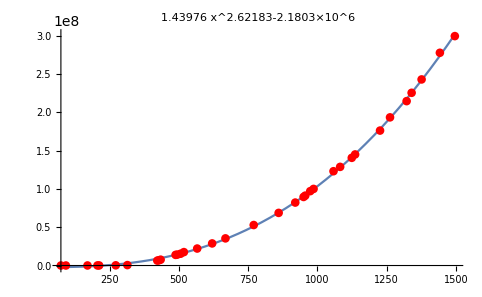

```mathematica
fitAndPlot[parse[s]]
```